#### A collection of challenging elastic maps T for finding the closest-Sigma-to-T. The issues pertain to using the built-in Mathematica function NMinimize. ES_FindSymGroups.nb calls GetTempAndθ0σ0ϕ0, which calls NMinimize. INSTRUCTIONS: Run common_funs.nb, ES_FindSymGroups.nb, BC_ChooseTmat.nb, then this notebook

```mathematica
WantDetails="WantDetails";
```

#### copied from ES_FindSymGroups.nb

```mathematica
(* GetTempAndθ0σ0ϕ0[Tmat_,Σ_]:=(Clear[θ,σ,ϕ];
temp[Tmat,Σ]= NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,σ,ϕ}],Σ],0≤θ≤2π&&-π≤σ≤π&&0≤ϕ≤π},{θ,σ,ϕ},Method->"RandomSearch"];
{θ0,σ0,ϕ0}=({θ,σ,ϕ}/.temp[Tmat,Σ][[2]]);
If[MemberQ[{XISO,MONO},Σ],σ0=0];) *)
```

#### Function to minimize over a localized square patch

```mathematica
Flocal[theta0_,phi0_,dtheta_,dphi_,Tmat_]:=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],theta0-dtheta≤θ≤theta0+dtheta&&phi0-dphi≤ϕ≤phi0+dphi},{θ,ϕ},Method->"RandomSearch"];
```

#### Adjust dθ based on how close the local minima are.

```mathematica
dtheta = 0.2π;
dphi=dtheta;
```

## Get the problematic map

```mathematica
Tmat = TmatMar17exact;
```

#### The problematic point is t = 0.2 on the segment from MONO to TRIG.

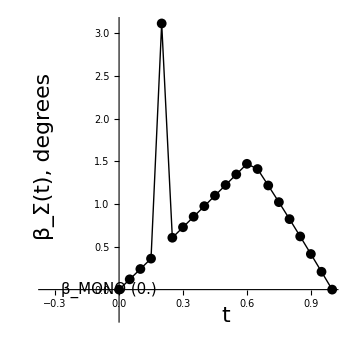

#### Reconstruct the problematic map.

```mathematica
MatrixNote[Tmat]
OutputFor[Tmat,XISO]
UXISO=UT[Tmat,XISO];
UforNM1=UXISO;
TMONO=ProjToVSigOfU[Tmat,UforNM1,MONO];
TTRIG=ProjToVSigOfU[Tmat,UforNM1,TRIG];
```

```mathematica
Tmatx=0.8TMONO+0.2TTRIG;
MatrixForm[TMONO]
MatrixForm[TTRIG]
PrintVoigt[Tmatx]
```

## Run NMinimize

#### The search with “RandomSearch” fails to find the global minimum (β = 3.11 vs β = 0.48):

```mathematica
OutputFor[Tmatx,MONO]
```

#### If we fix the seed to 0, we always get the same (incorrect) result:

```mathematica
Do[Print[NMinimize[{DistToVΣofU[Tmatx,UsHat[{θ,σ,φ}],MONO],0<=θ<=2 Pi&&-Pi<=σ<=Pi&&0<=φ<=Pi},{θ,σ,φ},Method->{"RandomSearch","RandomSeed"->0}]],{5}];
```

#### Now try a random integer. We always seem to get the true minimum. We can list (and save) the seed integer for each run.

```mathematica
NTRY=20;
```

```mathematica
GetTempAndΘ0Σ0Φ0[Tmat_,Σ_]:=Module[{randi,result,θ0,σ0,φ0},
Clear[θ,σ,φ];
randi=RandomInteger[100000];
result=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,σ,φ}],Σ],0<=θ<=2 Pi&&-Pi<=σ<=Pi&&0<=φ<=Pi},{θ,σ,φ},Method->{"RandomSearch","RandomSeed"->randi}];
{θ0,σ0,φ0}={θ,σ,φ}/. result[[2]];
(*If[MemberQ[{XISO,MONO},Σ],σ0=0];*)
{result[[1]],θ0,σ0,φ0,randi}]
```

```mathematica
Do[Print[GetTempAndΘ0Σ0Φ0[Tmatx,MONO]],{NTRY}]
```

#### CORRECT MINIMUM (β = 0.48): Lower left blue patch (and its antipode):

```mathematica
Flocal[0.4π,0.2π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
```

#### INCORRECT MINIMUM (β = 3.11): Blue patch (green point) on the equator (and its antipode):

```mathematica
Flocal[0.9π,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
```